```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
l=48;
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,l}];
Tc=Table[Max[Table[If[1/fpiall[[j]][[i]]<=2&&1/fpiall[[j]][[i+1]]>100,i,0],{i,1,Length[fpiall[[j]]]}]],{j,1,l}]
mub=Flatten[Table[i*11,{i,1,l}]]
```

{110,109,109,109,109,109,109,108,108,108,107,107,106,106,105,105,104,103,103,102,101,100,99,98,97,96,95,94,93,91,90,88,87,85,84,82,80,78,76,74,72,70,68,65,63,61,58,56}

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528}

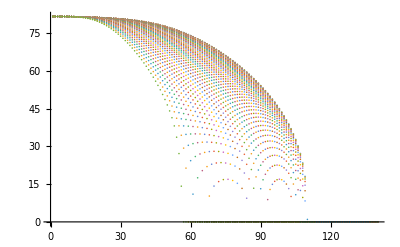

```mathematica
ListPlot[fpiall]
```

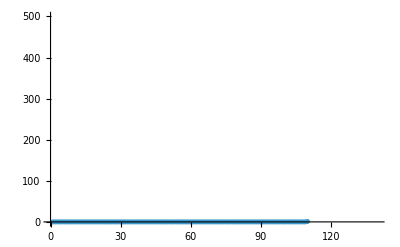

```mathematica
ListPlot[1/fpiall[[1]],PlotRange->{All,{0,500}}]
```

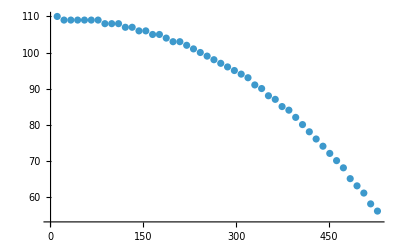

```mathematica
ListPlot[Transpose[{mub,Tc}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub,Tc}],a+b x^2+c x^4,{a,b,c},x]
```

{a→109.547,b→-0.000153578,c→-1.45967×10^-10}

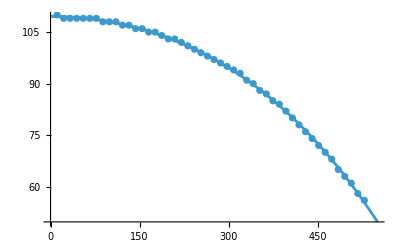

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,550}],ListPlot[Transpose[{mub,Tc}]]]
```

```mathematica
mub2=Table[i,{i,0,550,10}];
phaseboundary=Table[{mub2[[i]],a+b mub2[[i]]^2+c mub2[[i]]^4/.fitpd},{i,1,Length[mub2]}];
```

```mathematica
Export["pb.dat",phaseboundary]
```

pb.dat